```mathematica
SetDirectory[NotebookDirectory[]];
<< "OpticSimulate.wl"
```

```mathematica
Manipulate[
OpticRenderStatic[{4,3},{Mirror[0,0,Pi,1,3]}, Sources->{{x,y,theta,0.001, {Blue, 0.007}}}],
{x,-2,2},
{y,-1.5,1.5},
{theta, 0, 2 Pi}
]
```

```mathematica
""
```

1

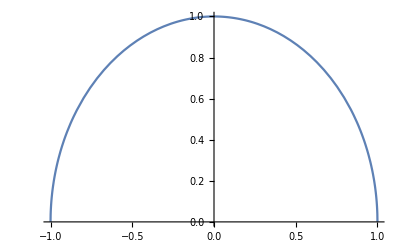

```mathematica
r = 1
exp:=Sqrt[r^2-x^2]-Sqrt[r^2-1^2]
Plot[exp, {x,-1,1}]
(* RegionPlot[0<=y<=exp,{x,-2,2},{y,-2,2}] *)
```

```mathematica
zz
```